Más sobre números

Al hacer cálculos con números enteros, Wolfram Language da respuestas exactas. Lo mismo sucede con las fracciones exactas.

Sumar 1/2+1/3 da el resultado exacto en forma de fracción:

```mathematica
1/2+1/3
```

5/6

Frecuentemente, lo que se desea es una aproximación numérica o decimal. Esto se obtiene usando la función N (por “numérica”).

Obtenga una respuesta numérica aproximada:

```mathematica
N[1/2+1/3]
```

0.833333

Si en la entrada aparece algún número decimal, Wolfram Language dará automáticamente una respuesta aproximada.

La presencia de un número decimal hace que el resultado sea aproximado:

```mathematica
1.8/2+1/3
```

1.23333

Es suficiente con poner un punto decimal al final de alguno de los números:

```mathematica
1/2.+1/3
```

0.833333

Wolfram Language puede trabajar con números de cualquier tamaño, con tal de que quepan en la memoria de la computadora que se esté usando.

Aquí aparece 2 elevado a la potencia 1000:

```mathematica
2^1000
```

10715086071862673209484250490600018105614048117055336074437503883703510511249361224931983788156958581275946729175531468251871452856923140435984577574698574803934567774824230985421074605062371141877954182153046474983581941267398767559165543946077062914571196477686542167660429831652624386837205668069376

Para obtener una aproximación numérica:

```mathematica
N[2^1000]
```

1.07151×10^301

Esta forma aproximada está dada en notación científica. Para ingresar algo en notación científica puede usarse *^.

Ingrese un número en notación científica:

```mathematica
2.7*^6
```

2.7×10^6

Aquellos números que sean de uso frecuente como π (pi) están ya construidos dentro de Wolfram Language.

Obtenga una aproximación numérica de π:

```mathematica
N[Pi]
```

3.14159

Wolfram Language puede calcular con precisión arbitraria y, por ejemplo, puede dar millones de dígitos para π, si se desea.

Calcule 250 dígitos de π:

```mathematica
N[Pi,250]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909

Existen muchas funciones en Wolfram Language que manejan números enteros. Hay también muchas funciones que manejan números reales (números aproximados con decimales). Por ejemplo, RandomReal, que produce números aleatorios reales.

Genere un número aleatorio real en el tramo de 0 a 10:

```mathematica
RandomReal[10]
```

2.08658

Genere 5 números aleatorios reales:

```mathematica
Table[RandomReal[10],5]
```

{4.15071,4.81048,8.82945,9.84995,9.08313}

Una forma alternativa de pedir 5 números aleatorios reales:

```mathematica
RandomReal[10,5]
```

{6.47318,3.29181,3.57615,8.11204,3.38286}

Números aleatorios reales en el tramo entre 20 y 30:

```mathematica
RandomReal[{20,30},5]
```

{24.1202,20.1288,20.393,25.6455,20.9268}

Wolfram Language contiene una cantidad enorme de funciones matemáticas nativas, desde las muy básicas hasta otras con un alto grado de sofisticación.

Encuentre el número primo en la posición 100:

```mathematica
Prime[100]
```

541

Encuentre el número primo en la posición un millón:

```mathematica
Prime[1000000]
```

15485863

Produzca un gráfico de los primeros 50 primos:

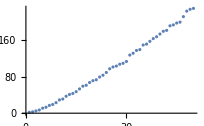

```mathematica
ListPlot[Table[Prime[n],{n,50}]]
```

Hay tres funciones muy comunes en situaciones prácticas, que son Sqrt (raíz cuadrada), Log10 (logaritmo en base 10) y Log (logaritmo natural).

La raíz cuadrada de 16 es 4:

```mathematica
Sqrt[16]
```

4

Si no se pide una aproximación numérica, se obtiene una fórmula exacta:

```mathematica
Sqrt[200]
```

10 √2

N produce una aproximación numérica:

```mathematica
N[Sqrt[200]]
```

14.1421

Los logaritmos son útiles cuando se manejan números con una amplia variabilidad en sus tamaños. Si se grafican las masas de los planetas, ListPlot no revela nada sobre los planetas anteriores a Júpiter. Pero ListLogPlot muestra muy claramente sus tamaños relativos.

Muestre un gráfico ordinario de las masas de los planetas:

```mathematica
ListPlot[EntityClass["Planet",All]["Mass"]]
```

-Graphics-

Muestre un gráfico en escala logarítmica:

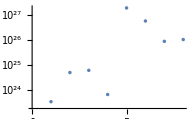

```mathematica
ListLogPlot[EntityClass["Planet",All]["Mass"]]
```

Hay unas cuantas funciones más que aparecen frecuentemente en la programación común. Primero, la función, casi trivial, Abs, que encuentra el valor absoluto, o parte positiva, de un número.

Abs realmente lo que hace es desechar los signos menos:

```mathematica
{Abs[3],Abs[-3]}
```

{3,3}

Enseguida está Round, que efectúa el redondeo al entero más cercano.

Round redondea al entero más cercano:

```mathematica
{Round[3.2],Round[3.4],Round[3.6],Round[3.9]}
```

{3,3,4,4}

Otra función muy útil es Mod. Cuando se están contando los minutos en una hora, al llegar a 60 se desea comenzar de nuevo desde 0, y eso es lo que hace Mod.

Calcule una secuencia de números mod 60:

```mathematica
{Mod[50,60],Mod[55,60],Mod[60,60],Mod[65,60],Mod[70,60]}
```

{50,55,0,5,10}

Vocabulario

N[expr] |   | aproximación numérica 
Pi |   | el número π (pi)≃3.14 
Sqrt[x] |   | raíz cuadrada
Log10[x] |   | logaritmo en base 10 
Log[x] |   | logaritmo natural (ln) 
Abs[x] |   | valor absoluto (desechar los signos menos) 
Round[x] |   | redondea al entero más cercano 
Prime[n] |   | n-ésimo número primo
Mod[x,n] |   | módulo (“aritmética del reloj”) 
RandomReal[max] |   | número real aleatorio entre 0 y max 
RandomReal[max,n] |   | lista de n números reales aleatorios
ListLogPlot[data] |   | produce la gráfica en escala logarítmica

"14 Exercises Available"
"with 4 extras" | "Get Started »"

Encuentre √2 con una precisión de 500 dígitos. »

| Expected output: |  
  | 1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309122970249248360558507372126441214970999358314132226659275055927557999505011527820605714701095599716059702745345968620147285174186408891986095523292304843087143214508397626036279952514079896872533965463318088296406206152583523950547457502877599617298355752203375318570113543746034084988471603868999706990048150305440277903164542478230684929369186215805784631115966687130130156185689872372 |

Genere 10 números reales aleatorios entre 0 y 1. »

| Sample expected output: |  
  | {0.981757,0.501571,0.0805282,0.0247074,0.0663221,0.812191,0.929721,0.949164,0.674154,0.0702841} |

Haga un gráfico de 200 puntos con coordenadas reales x e y aleatorias entre 0 y 1. »

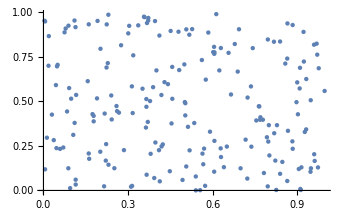
| Sample expected output: |  
  | -Graphics- |

Cree una caminata aleatoria usando AnglePath y 1000 números reales aleatorios entre 0 y 2π. »

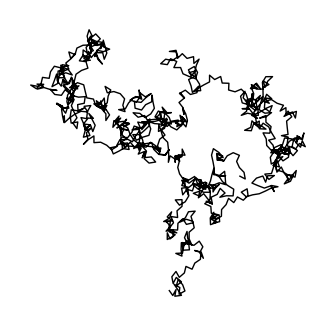
| Sample expected output: |  
  | -Graphics- |

Haga una tabla de Mod[n^2,10] para n de 0 a 30. »

| Expected output: |  
  | {0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0} |

Haga un gráfico con los puntos unidos de Mod[n^n,10] para n de 1 a 100. »

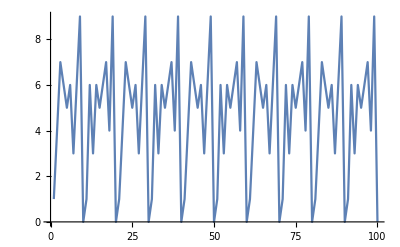
| Expected output: |  
  | -Graphics- |

Haga una tabla de las primeras 10 potencias de π, redondeadas a enteros. »

| Expected output: |  
  | {3,10,31,97,306,961,3020,9489,29809,93648} |

Construya un grafo conectando n con Mod[n^2,100] para n desde 0 a 99. »

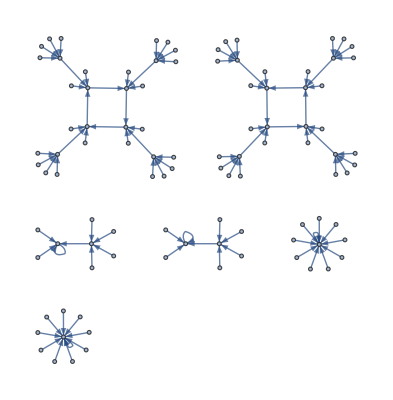
| Expected output: |  
  | -Graphics- |

Genere los gráficos de 50 círculos con coordenadas reales aleatorias de 0 a 10, con radios reales aleatorios de 0 a 2, y de colores aleatorios. »

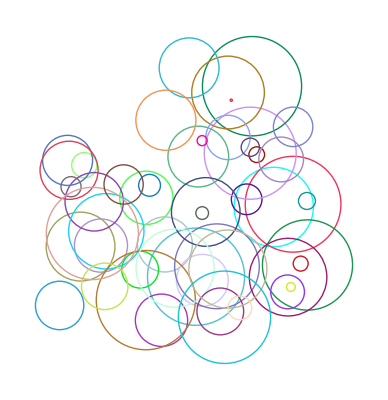
| Sample expected output: |  
  | -Graphics- |

Presente gráficamente el n-ésimo primo dividido por n*log(n), para n del 2 al 1000. »

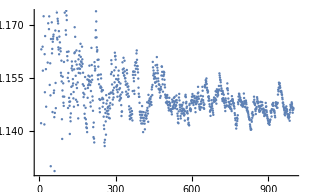
| Expected output: |  
  | -Graphics- |

Presente un gráfico con los puntos unidos de las diferencias entre primos consecutivos hasta el 100. »

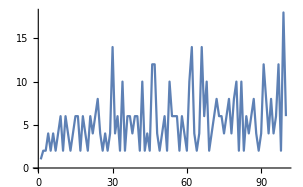
| Expected output: |  
  | -Graphics- |

Genere una secuencia de 20 notas C central (do central), de duraciones aleatorias entre 0 y 0.5 segundos. »

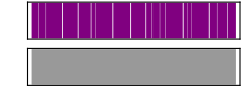
| Sample expected output: |  
  | -Graphics- |

Genere un gráfico de arreglo para Mod[i,j] con i y j hasta 50. »

| Expected output: |  
  | -Graphics- |

Construya una lista de gráficos de arreglo de x^y mod n, con n de 2 a 10, para x e y hasta 50. »

| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Use Round para calcular la parte fraccionaria de π con 50 dígitos. »

| Expected output: |  
  | 0.14159265358979323846264338327950288419716939937511 |

Encuentre la suma de los primeros 1000 números primos. »

| Expected output: |  
  | 3682913 |

Construya una lista con los primeros 100 primos módulo 4. »

| Expected output: |  
  | {2,3,1,3,3,1,1,3,3,1,3,1,1,3,3,1,3,1,3,3,1,3,3,1,1,1,3,3,1,1,3,3,1,3,1,3,1,3,3,1,3,1,3,1,1,3,3,3,3,1,1,3,1,3,1,3,1,3,1,1,3,1,3,3,1,1,3,1,3,1,1,3,3,1,3,3,1,1,1,1,3,1,3,1,3,3,1,1,1,3,3,3,3,3,3,3,1,1,3,1} |

Forme la lista de los primeros 10 000 primos módulo 4, multiplíquelos por 90° y cree una trayectoria angular con el resultado. »

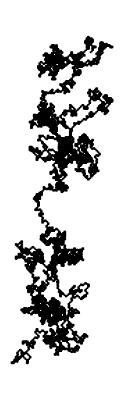
| Expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿Se pueden dar ejemplos de funciones matemáticas en Wolfram Language?

De las matemáticas escolares estándar, se pueden dar algunos ejemplos tales como Sin, Cos, ArcTan, Exp, así como GCD, Factorial, Fibonacci. De la física, la ingeniería y las matemáticas superiores, algunos tales como Gamma (“función gamma”), BesselJ (“función de Bessel”), EllipticK (“integral elíptica”), Zeta (“función zeta de Riemann”), PrimePi, EulerPhi. De la estadística, algunos otros tales como Erf, NormalDistribution, ChiSquareDistribution. En total, centenares de ellos.

¿Qué es la precisión de un número?

Es el número total de dígitos decimales que aparecen en ese número. N[100/3,5] da 33.333, que tiene una precisión de 5 dígitos. El número 100/3 es exacto; N[100/3,5] lo aproxima con una precisión de 5 dígitos.

¿Qué significa  al final de cada renglón en un número muy largo?

Indica que el número continúa en el siguiente renglón, como el guión en un texto.

¿Se puede trabajar con números en bases diferentes de 10?

Sí. Si hubiera que escribir un número en base 16, se haría como 16^^ffa5. Se encuentran los dígitos usando IntegerDigits[655,16].

¿Puede Wolfram Language manejar números complejos?

Desde luego. El símbolo I (“i” mayúscula) representa la raíz cuadrada de −1.

¿Por qué N[1.5/7,100] no da un resultado con 100 dígitos?

Porque 1.5 es un número aproximado con una precisión mucho menor de 100 dígitos. Pero, por ejemplo, N[15/70,100] da un número con una precisión de 100 dígitos.

Notas técnicas

Wolfram Language efectúa “computación con precisión arbitraria”, es decir, puede conservar tantos dígitos en un número como se quiera.

Cuando se genera un número con cierta precisión usando N, Wolfram Language llevará automáticamente la cuenta de cómo afecta dicha precisión a los cálculos, de tal modo que uno no tiene que efectuar su propio análisis de los errores de redondeo.

Al ingresar un número tal como 1.5, se supone que tiene la “precisión de máquina” nativa de los números en la computadora que se esté usando (por lo general, unos 16 dígitos, aunque usualmente solo se muestran 6). Se usa 1.5`100 para especificar una precisión de 100 dígitos.

Si se ingresa un número exacto (tal como 4 o 2/3 o Pi), Wolfram Language trata siempre de dar una salida exacta. Pero si la entrada contiene un número aproximado (como 2.3) o, si se usa N, utilizará la aproximación numérica.

La aproximación numérica es muchas veces crucial para hacer posibles los cálculos en gran escala.

PrimeQ comprueba si un número es primo (ver la Sección 28). FactorInteger encuentra los factores de un entero.

RandomReal puede generar números con distribuciones diferentes de la uniforme. Por ejemplo, RandomReal[NormalDistribution[ ]] genera números con una distribución normal.

Round redondea al entero más cercano (arriba o abajo); Floor siempre redondea hacia abajo; Ceiling siempre redondea hacia arriba.

RealDigits es el análogo de IntegerDigits para números reales.

Para explorar más

Guía para números en Wolfram Language »

Guía para funciones matemáticas en Wolfram Language »